Okeefe Niemann
5/15/2014
PHYS 115
1281465

                                                                                  Assignment #6

### Question 1

```mathematica
200!
```

788657867364790503552363213932185062295135977687173263294742533244359449963403342920304284011984623904177212138919638830257642790242637105061926624952829931113462857270763317237396988943922445621451664240254033291864131227428294853277524242407573903240321257405579568660226031904170324062351700858796178922222789623703897374720000000000000000000000000000000000000000000000000

### Question 2

```mathematica
N[50000!]
```

3.34732050959714×10^213236

### Question 3

Input :

```mathematica
#include <stdio.h>
#include <math.h>

double f(double x)
{
	return log10(x);
}

main()
{
	int i, exponent, argument = 50000;
	double mantissa, logfactorial, logmantissa;

	//computes log base 10 of the factorial
	for(i = argument; i > 0; i--)
	{
		logfactorial += f(i);         
	}

	
	printf("log(%d!) = %f  \n", argument, logfactorial);

	exponent = logfactorial;               
	//computes the exponent of scientific notation 
	logmantissa = logfactorial - exponent; 
	//finds what's "left over" after subtracting exponent from log
	mantissa = pow(10, logmantissa); 
	//raises  the "leftovers" by a power of 10 to find coefficient

	printf("%d! = %f + 10^%d\n", argument, mantissa, exponent);

return 0;
}
```

Output:
	log(50000!) = 213236.524697  
	50000! = 3.347321 + 10^213236

Comment: The technique to solving this factorial in C is understanding the product property of logarithms, which allows the multiplied values in its argument to be seperated into the sum of their logarithmic values. After this sum is computed, the next step is to splt the value into a sum of an integer and a decimal. When these two additive values are raised by base ten, they then multiply. The integer will then be the power in which 10 is raised, while 10 raised to the decimal will take the position of the mantissa in floating point form.

### Question 4

```mathematica
N[E^(Pi*√163), 29] //AccountingForm
```

262537412640768744.00000000000

```mathematica
N[E^(Pi*√163), 30] //AccountingForm
```

262537412640768743.999999999999

As shown above, the function rounds off to an integer until it’s output is evaluated to 30 decimal places.

### Question 5

```mathematica
TableForm[x /. NSolve[x^7 + x^5 + 2 x^3 + x^2 + 1 == 0]]
```

-0.812432
-0.640787-1.07931 ⅈ
-0.640787+1.07931 ⅈ
0.254825-0.700968 ⅈ
0.254825+0.700968 ⅈ
0.792178-0.881387 ⅈ
0.792178+0.881387 ⅈ

### Question 6

```mathematica
NIntegrate[HermiteH[4,x]^2 Exp[-x^2], {x, -Infinity, Infinity}]
```

680.622

### Question 7

```mathematica
ans[x_]=
y[x] /.
NDSolve[{y''[x] == 2x + y[x] + 3y'[x], y[2]==1, y'[2] == -1}, y, {x, 2.0, 2.3}][[1]];
```

```mathematica
ans[2.2]
```

0.851094

```mathematica
Show[Plot[ans[x], {x, 2.0, 2.3}],ImageSize->Large]
```

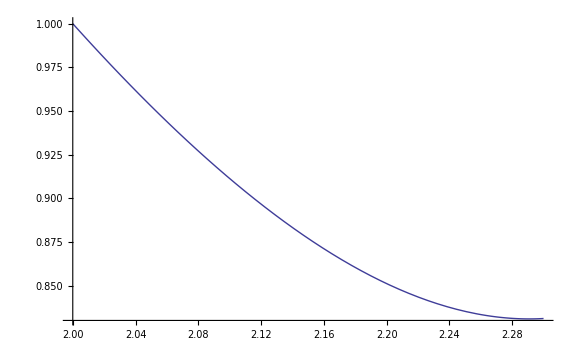

### Question 8

```mathematica
TableForm[{{x,y}/. Solve[{4 x+5 y==5,6 x+7 y==7}, {x,y}][[1]]}, TableHeadings -> {None, {"x", "y"}}]
```

x | y
0 | 1

### Question 9

```mathematica
x /. Solve[{Sqrt[x + 2] + 4 == x}, {x}][[1]]
```

7

### Question 10

```mathematica
Limit[1/(E^x - E^(x - x^(-2))), x -> Infinity]
```

0

### Question 11

```mathematica
y[x] /. DSolve[y''[x] - 6y'[x] + 13y[x] == (E^x) Cos[x], y, x][[1]]//Simplify
```

1/65 ⅇ^x (65 ⅇ^(2 x) C[2] Cos[2 x]-4 Sin[x]+Cos[x] (7+130 ⅇ^(2 x) C[1] Sin[x]))

### Question 12

```mathematica
xlist = Table[n, {n,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
ylist = Table[n^2, {n,0,10}]
```

{0,1,4,9,16,25,36,49,64,81,100}

```mathematica
Transpose[{xlist,ylist}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

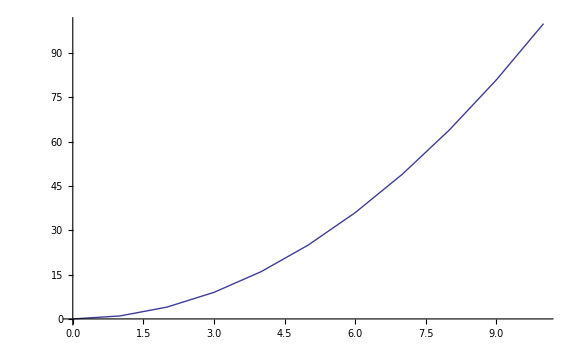

```mathematica
ListPlot[{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}},Joined->True]
```

### Question 13

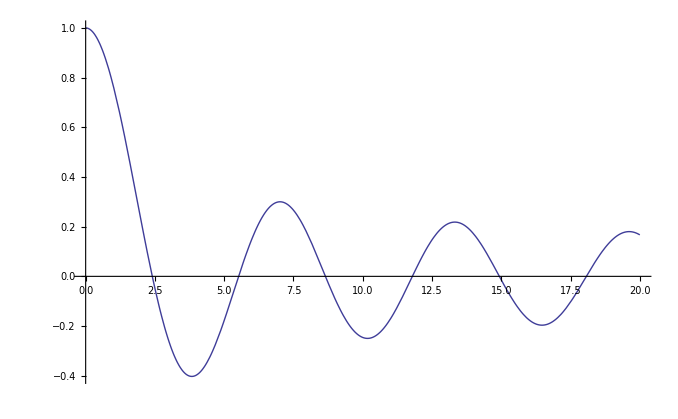

```mathematica
Plot[BesselJ[0, x], {x, 0, 20}]
```

```mathematica
TableForm[{x /.FindRoot[BesselJ[0, x], {x,{2,5,9,12,15}}]}, TableHeadings->{{Roots}, {x1,x2, x3, x4, x5}}]
```

| x1 | x2 | x3 | x4 | x5
Roots | 2.40483 | 5.52008 | 8.65373 | 11.7915 | 14.9309

### Question 14

```mathematica
u0 = 2^(-0/2)(Pi 0!^2)^(-1/4) HermiteH[0,x] Exp[-(x^2)/2];
```

```mathematica
u2 =2^(-2/2)(Pi 2!^2)^(-1/4) HermiteH[2,x] Exp[-(x^2)/2];
```

```mathematica
u3 = 2^(-3/2)(Pi 3!^2)^(-1/4) HermiteH[3,x] Exp[-(x^2)/2];
```

```mathematica
u4 = 2^(-4/2)(Pi 4!^2)^(-1/4) HermiteH[4,x] Exp[-(x^2)/2];
```

Part a

```mathematica
Integrate[u3^2, {x, -Infinity, Infinity}]
```

1

Part b

```mathematica
Integrate[u3 u2, {x, -Infinity, Infinity}]
```

0

Part c

0

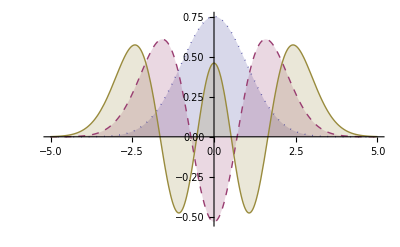

```mathematica
Plot[{u0, u2, u4}, {x, -5, 5}, PlotStyle ->  {Dotted, Dashed, Thick}, Filling -> Axis ]
```

u0: Blue,    u2: Magenta,  u4: Brown

### Question 15

```mathematica
nans[t_] = i[t] /.
NDSolve[{i'[t] + 2i[t] == Sin[t], i[0]== 0}, i[t], {t, 0, 1.1}][[1]]
```

InterpolatingFunction[{{0.,1.1}},<>][t]

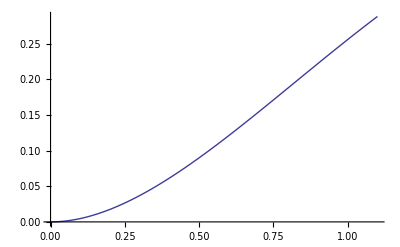

```mathematica
Plot[nans[t], {t,0,1.1}]
```

```mathematica
aans[t_] = i[t] /. 
DSolve[{i'[t] + 2i[t] == Sin[t], i[0]== 0}, i, t][[1]] // Simplify
```

1/5 (ⅇ^(-2 t)-Cos[t]+2 Sin[t])

```mathematica
numeric= Table[nans[t],  {t, 0, 1, .1}];
```

```mathematica
analytic = Table[aans[t], {i, 0, 9}, {t, i/10, i/10 +.1}];
```

```mathematica
TableForm[Table[{j, numeric[[j]], analytic[[j]]}, {j, 1, 10}], TableHeadings -> {None, {"t","Numeric", "Analytic"}}]
```

t | Numeric | Analytic
1 | 0. | 0
2 | 0.0046787 | 1/5 (1/ⅇ^(1/5)-Cos[1/10]+2 Sin[1/10])
3 | 0.0175184 | 1/5 (1/ⅇ^(2/5)-Cos[1/5]+2 Sin[1/5])
4 | 0.0369031 | 1/5 (1/ⅇ^(3/5)-Cos[3/10]+2 Sin[3/10])
5 | 0.0614209 | 1/5 (1/ⅇ^(4/5)-Cos[2/5]+2 Sin[2/5])
6 | 0.0898296 | 1/5 (1/ⅇ-Cos[1/2]+2 Sin[1/2])
7 | 0.121029 | 1/5 (1/ⅇ^(6/5)-Cos[3/5]+2 Sin[3/5])
8 | 0.154038 | 1/5 (1/ⅇ^(7/5)-Cos[7/10]+2 Sin[7/10])
9 | 0.18798 | 1/5 (1/ⅇ^(8/5)-Cos[4/5]+2 Sin[4/5])
10 | 0.222069 | 1/5 (1/ⅇ^(9/5)-Cos[9/10]+2 Sin[9/10])